# Sparse Approximate Inverse

## Intro

Suppose we have an n×n sparse matrix A then we can find the sparse matrix P (with a specified sparsity pattern) that minimizes 
	||P.A-I(||)_F^2.
Specifically if 𝒫 is a sparsity pattern class then 
	argmin_(P∈𝒫)||P.A-I(||)_F^2
can be computed relatively efficiently.  The minimum is well defined because the cost function is a positive definite sum of squares in the non-zero entries of P. The minimizer is unique unless the sum of squares is degenerate!

Note, if A is invertible and we consider dense matrices the minimum zero is attained when P=A^-1.

### Parallel Algorithm

Of course, the product P.A is computed by running along the rows of P and down the columns of A.  So each row of P.A depends only on the corresponding row of P. Splitting the cost function up by row shows that each row of P is determined by minimizing the reduced cost function
	 argmin_(P⟦i,:⟧∈𝒫_i)||P⟦i,:⟧.A-e_i(||)_^2.
In other words, each row of P is determined by a substantially smaller least squares problem defined by the product of a sparse vector and the sparse matrix A.

If row i of P has nz_i allowed non-zeros then the LS problem for row i is n×nz_i.  The problems for each row are completely independent!  They require no communication.  Such a problem is called embarrassingly parallel.

### Small Scale Demo

Suppose my matrix is

```mathematica
A=({{2.0, 0, 0, 1.2}, {1.2, 4.0, 0, 0}, {0, 0, 3.1, 0.1}, {0, 0.1, 0, 0.6}});
```

I can assume that my P has the same sparsity pattern as A in other words.

```mathematica
P=({{p11, 0, 0, p14}, {p21, p22, 0, 0}, {0, 0, p33, p34}, {0, p42, 0, p44}});
Id=IdentityMatrix[4];
```

Then the 4 partial objective functions are

```mathematica
Table[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
Simplify[temp.temp],
{i,1,4}]
```

{1.+5.44 p11^2+0.37 p14^2+p11 (-4.+1.44 p14),1.+5.44 p21^2-8. p22+4.8 p21 p22+17.44 p22^2,1.+9.62 p33^2+p33 (-6.2+0.12 p34)+0.37 p34^2,1.+17.44 p42^2-1.2 p44+0.8 p42 p44+0.37 p44^2}

The minimizer of each is easily computed by setting the derivatives equal to zero.

```mathematica
ParallelTable[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
quad=temp.temp;
Minimize[quad,Variables[quad]],
{i,1,4}]
```

{{0.00963597,{p11→0.495182,p14→-0.963597}},{0.0232692,{p21→-0.107728,p22→0.244183}},{0.0000281231,{p33→0.322572,p34→-0.0523089}},{0.00228833,{p42→-0.0381388,p44→1.66285}}}

Of course, for a small problem there is no need to split the sum up like this and you can perform the “big” minimization on the sum.

```mathematica
quad=Sum[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
temp.temp,
{i,1,4}];
{val,sub}=Minimize[quad,Variables[quad]]
```

{0.0352216,{p11→0.495182,p14→-0.963597,p21→-0.107728,p22→0.244183,p33→0.322572,p34→-0.0523089,p42→-0.0381388,p44→1.66285}}

Whichever way you do it you get something that you might hope was a decent preconditioner.  Of course the way to check how good a preconditioner it is to check the spectrum of P.A

```mathematica
PStar=P/.sub;
Eigenvalues[PStar.A]
SingularValueList[PStar.A]
```

{1.00923+0.105776 ⅈ,1.00923-0.105776 ⅈ,0.999972+0. ⅈ,0.946351+0. ⅈ}

{1.0525,1.00057,0.998797,0.926438}

### Larger Scale Computation

For a larger sparse matrix there will be lots of structural zeros in 
	P.A
which do not need to be computed or summed.  Efficient algorithms avoid this unnecessary work using a variety of tricks.   Here is an attempt at avoiding some of this work in a simple way on a familiar matrix.

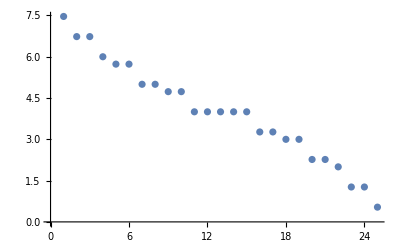

```mathematica
n=5;
m=n^2;
A=SparseArray[{},{m,m}];
ijTok[i_,j_,n_]:=i+(j-1)*n;
Do[
k=ijTok[i,j,n];
A⟦k,k⟧=4;
If[1≤i+1≤n,A⟦k,ijTok[i+1,j,n]⟧=-1.0];
If[1≤i-1≤n,A⟦k,ijTok[i-1,j,n]⟧=-1.0];
If[1≤j+1≤n,A⟦k,ijTok[i,j+1,n]⟧=-1.0];
If[1≤j-1≤n,A⟦k,ijTok[i,j-1,n]⟧=-1.0],
{i,1,n},{j,1,n}]
ListPlot[Eigenvalues[A]]
```

```mathematica
ArrayRules[A]
```

{{1,1}→4,{1,2}→-1.,{1,6}→-1.,{2,2}→4,{2,3}→-1.,{2,1}→-1.,{2,7}→-1.,{3,3}→4,{3,4}→-1.,{3,2}→-1.,{3,8}→-1.,{4,4}→4,{4,5}→-1.,{4,3}→-1.,{4,9}→-1.,{5,5}→4,{5,4}→-1.,{5,10}→-1.,{6,6}→4,{6,7}→-1.,{6,11}→-1.,{6,1}→-1.,{7,7}→4,{7,8}→-1.,{7,6}→-1.,{7,12}→-1.,{7,2}→-1.,{8,8}→4,{8,9}→-1.,{8,7}→-1.,{8,13}→-1.,{8,3}→-1.,{9,9}→4,{9,10}→-1.,{9,8}→-1.,{9,14}→-1.,{9,4}→-1.,{10,10}→4,{10,9}→-1.,{10,15}→-1.,{10,5}→-1.,{11,11}→4,{11,12}→-1.,{11,16}→-1.,{11,6}→-1.,{12,12}→4,{12,13}→-1.,{12,11}→-1.,{12,17}→-1.,{12,7}→-1.,{13,13}→4,{13,14}→-1.,{13,12}→-1.,{13,18}→-1.,{13,8}→-1.,{14,14}→4,{14,15}→-1.,{14,13}→-1.,{14,19}→-1.,{14,9}→-1.,{15,15}→4,{15,14}→-1.,{15,20}→-1.,{15,10}→-1.,{16,16}→4,{16,17}→-1.,{16,21}→-1.,{16,11}→-1.,{17,17}→4,{17,18}→-1.,{17,16}→-1.,{17,22}→-1.,{17,12}→-1.,{18,18}→4,{18,19}→-1.,{18,17}→-1.,{18,23}→-1.,{18,13}→-1.,{19,19}→4,{19,20}→-1.,{19,18}→-1.,{19,24}→-1.,{19,14}→-1.,{20,20}→4,{20,19}→-1.,{20,25}→-1.,{20,15}→-1.,{21,21}→4,{21,22}→-1.,{21,16}→-1.,{22,22}→4,{22,23}→-1.,{22,21}→-1.,{22,17}→-1.,{23,23}→4,{23,24}→-1.,{23,22}→-1.,{23,18}→-1.,{24,24}→4,{24,25}→-1.,{24,23}→-1.,{24,19}→-1.,{25,25}→4,{25,24}→-1.,{25,20}→-1.,{_,_}→0}

Then the 4 partial objective functions are

```mathematica
Table[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
Simplify[temp.temp],
{i,1,4}]
```

{1.+5.44 p11^2+0.37 p14^2+p11 (-4.+1.44 p14),1.+5.44 p21^2-8. p22+4.8 p21 p22+17.44 p22^2,1.+9.62 p33^2+p33 (-6.2+0.12 p34)+0.37 p34^2,1.+17.44 p42^2-1.2 p44+0.8 p42 p44+0.37 p44^2}

The minimizer of each is easily computed by setting the derivatives equal to zero.

```mathematica
ParallelTable[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
quad=temp.temp;
Minimize[quad,Variables[quad]],
{i,1,4}]
```

{{0.00963597,{p11→0.495182,p14→-0.963597}},{0.0232692,{p21→-0.107728,p22→0.244183}},{0.0000281231,{p33→0.322572,p34→-0.0523089}},{0.00228833,{p42→-0.0381388,p44→1.66285}}}

Of course, for a small problem there is no need to split the sum up like this and you can perform the “big” minimization on the sum.

```mathematica
quad=Sum[
temp=P⟦i,All⟧.A-Id⟦i,All⟧;
temp.temp,
{i,1,4}];
{val,sub}=Minimize[quad,Variables[quad]]
```

{0.0352216,{p11→0.495182,p14→-0.963597,p21→-0.107728,p22→0.244183,p33→0.322572,p34→-0.0523089,p42→-0.0381388,p44→1.66285}}

Whichever way you do it you get something that you might hope was a decent preconditioner.  Of course the way to check how good a preconditioner it is to check the spectrum of P.A

```mathematica
PStar=P/.sub;
Eigenvalues[PStar.A]
SingularValueList[PStar.A]
```

{1.00923+0.105776 ⅈ,1.00923-0.105776 ⅈ,0.999972+0. ⅈ,0.946351+0. ⅈ}

{1.0525,1.00057,0.998797,0.926438}